Polynomial Blending

```mathematica
left[s_]:=lb+lm s
right[s_]:=rb+rm (s+(lb-rb+(lm -rm)sMid)/rm)
blend[s_]:=a s^5+b s^4+c s^3+d s^2+e s+f
```

```mathematica
resultBlendAll=Solve[{
blend[sMid-sAbs]==left[sMid-sAbs],
blend'[sMid-sAbs]==left'[sMid-sAbs],
blend''[sMid-sAbs]==left''[sMid-sAbs],
blend[sMid+sAbs]==right[sMid+sAbs],
blend'[sMid+sAbs]==right'[sMid+sAbs],
blend''[sMid+sAbs]==right''[sMid+sAbs],
blend[sMid]-left[sMid]==maxDiff
},{a,b,c,d,e,f,sAbs}];
```

```mathematica
resultBlend=Solve[{
blend[sMid-sAbs]==left[sMid-sAbs],
blend'[sMid-sAbs]==left'[sMid-sAbs],
blend''[sMid-sAbs]==left''[sMid-sAbs],
blend[sMid+sAbs]==right[sMid+sAbs],
blend'[sMid+sAbs]==right'[sMid+sAbs],
blend''[sMid+sAbs]==right''[sMid+sAbs]
},{a,b,c,d,e,f}];
```

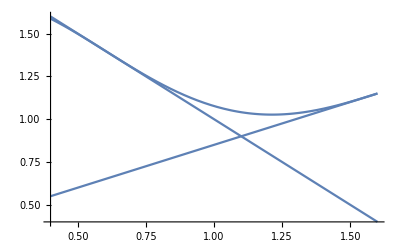

```mathematica
Plot[{
left[s],
right[s],
blend[s]/.resultBlend/.{sAbs->0.5}
}/.{lb->2,lm->-1,sMid->1.1,rb->1,rm->0.5},{s,0.4,1.6}]
```

```mathematica
ToString[Simplify[resultBlend[[1,6,2]]],CForm]
CopyToClipboard[%]
```

lb - ((lm - rm)*Power(sAbs - sMid,3)*(3*sAbs + sMid))/(16.*Power(sAbs,3))